```mathematica
(*** Soliton ***)
    * Solitons are the solution of non-linear dispersive partial differential equations.
* They are localized within a region.
* They Collide with other solitons and remain unchanged in shape.
* They retained their speed after interaction with other solitons.
```

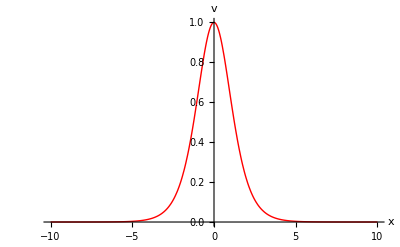

```mathematica
(* Single Soliton *)t=0;v=2;
Plot[v/2* Sech[Sqrt[v]/2*(x+v*t)]^2,{x,-10,10},PlotStyle->{{Red,Thick}},PlotRange->
All,AxesLabel->{"x" , "v"}]
```

```mathematica
(* Multi Soliton *)
```

```mathematica
Animation of Soliton for KDV Equation ;
v=2;
Animate[Plot[(v/2* Sech[Sqrt[v]/2*(x+v*t)]^2+5  v/2* Sech[Sqrt[v]/2*(x-v*t)]^2),{x,-20,20},PlotStyle->{{Red,Thick}},PlotRange->
All,AxesLabel->{"x" , "v"}],{t,-7,7}]
```

```mathematica
Animation of Soliton for NLS Equation;
t=0;u=1;
Animate[Plot[(5 *Sech[(x+u*t)]+ Sech[(x-u*t)]),{x,-30,30},PlotStyle->{{Green,Thick}},PlotRange->All,AxesLabel->{"x" , "u"}],{t,-20,20}]
```

```mathematica
Solitonic Solution  of Sine-Gordon Eq  ;
Soliton and Anti-Soliton;
t=0;c=0.7;
Animate[Plot[ ( - 8*c*c*Sinh[(c t)/Sqrt[1-c*c]]*Sinh[(x)/Sqrt[1-c*c]]/(Sqrt[1-c*c]*(1-c*c+Cosh[2*c*t]/Sqrt[1-c*c]+c*c  Cosh[2x/Sqrt[1-c*c]])
)-  8*c*c*Sinh[(c t)/Sqrt[1-c*c]]*Sinh[(x)/Sqrt[1-c*c]]/(Sqrt[1-c*c]*(1-c*c+Cosh[2*c*t]/Sqrt[1-c*c]+c*c  Cosh[2x/Sqrt[1-c*c]])
)),{x,-30,30},PlotStyle->{{Blue,Thick}},PlotRange->All],{t,-20,20}]
```